# Data Librarian -Figures-

```mathematica
SetDirectory["/Users/kouamano/TEXT/Data_librarian/Sections"]
```

/Users/kouamano/TEXT/Data_librarian/Sections

## Programs

Cons Cell

```mathematica
recBox[{x1_,y1_},{x2_,y2_}]:=Line[{{x1,y1},{x2,y1},{x2,y2},{x1,y2},{x1,y1}}]
```

```mathematica
recBox[{x1_,y1_},{x2_,y2_},tx_]:={Line[{{x1,y1},{x2,y1},{x2,y2},{x1,y2},{x1,y1}}],Text[tx,{(x1+x2)/2,(y1+y2)/2}]}
```

```mathematica
recBox[{x1_,y1_},{x2_,y2_},{tx_,s_}]:={Line[{{x1,y1},{x2,y1},{x2,y2},{x1,y2},{x1,y1}}],Text[Style[tx,FontSize->s],{(x1+x2)/2,(y1+y2)/2}]}
```

```mathematica
circleText[cood_,r_,tx_]:={Circle[cood,r],Text[tx,cood]}
```

```mathematica
circleText[cood_,r_,{tx_,s_}]:={Circle[cood,r],Text[Style[tx,FontSize->s],cood]}
```

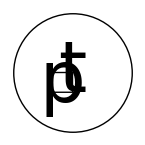

```mathematica
Graphics[{recBox[{0,0},{1,1},{"p",120}],circleText[{1,1},3,{"t",100}]}]
```

```mathematica
cons[{},cood_]:={recBox[cood,cood+1],recBox[cood+{1,0},cood+{2,1}],Line[{cood+{1.5,0.5},cood+{2.5,0.5}}]}
```

```mathematica
cons[{,},cood_]:={recBox[cood,cood+1],recBox[cood+{1,0},cood+{2,1}],Line[{cood+{1.5,0.5},cood+{2.5,0.5}}],Line[{cood+0.5,cood+0.5+{0,-1}}]}
```

```mathematica
cons[{Null},cood_]:={recBox[cood,cood+1],recBox[cood+{1,0},cood+{2,1}],Line[{cood+{1,0},cood+{2,1}}],Line[{cood+0.5,cood+0.5+{0,-1}}]}
```

```mathematica
cons[{x_String},cood_]:={recBox[cood,cood+1],recBox[cood+{1,0},cood+{2,1}],Line[{cood+{1,0},cood+{2,1}}],Line[{cood+0.5,cood+0.5+{0,-1}}],circleText[cood+0.5+{0,-1.5},0.5,{x,16}]}
```

```mathematica
cons[{{x_}},cood_]:={recBox[cood,cood+1],recBox[cood+{1,0},cood+{2,1}],
Line[{cood+{1,0},cood+{2,1}}],
Line[{cood+0.5,cood+0.5+{0,-1}}],
cons[{x},cood+{0,-1.5}]
}
```

```mathematica
cons[{x_String,y__String},cood_]:={recBox[cood,cood+1],recBox[cood+{1,0},cood+{2,1}],Line[{cood+{1.5,0.5},cood+{1.5,0.5}+{1,0}}],Line[{cood+0.5,cood+0.5+{0,-1}}],circleText[cood+0.5+{0,-1.5},0.5,{x,16}],cons[{y},cood+{2.5,0}]}
```

```mathematica
cons[{{x_,y__}},cood_]:={recBox[cood,cood+1],recBox[cood+{1,0},cood+{2,1}],
Line[{cood+{1,0},cood+{1,0}+1}],
Line[{cood+0.5,cood+0.5+{0,-1}}],
cons[{x,y},cood+{0,-1.5}]
(*cons[{y},cood+{2.5,0}]*)
}
```

## Figures

### Cons cell

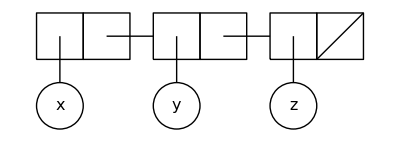

```mathematica
Graphics[cons[{"x","y","z"},{1,1}]]
```

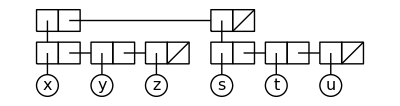

```mathematica
Graphics[{cons[{,},{1,1}],cons[{"x","y","z"},{1,-0.5}],Line[{{3.5,1.5},{9,1.5}}],cons[{Null},{9,1}],cons[{"s","t","u"},{9,-0.5}]}]
```

### Fig[zu-cell]

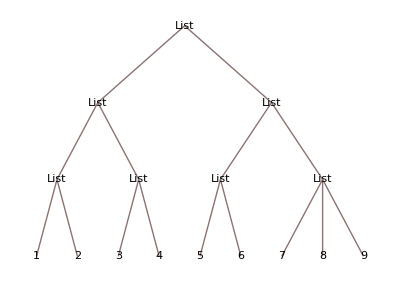

```mathematica
TreeForm[{{{1,2},{3,4}},{{5,6},{7,8,9}}}]
```

```mathematica
li={1,2,{3,4}}
```

{1,2,{3,4}}

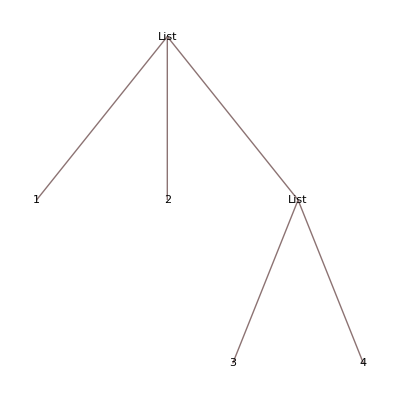

```mathematica
TreeForm[li]
```

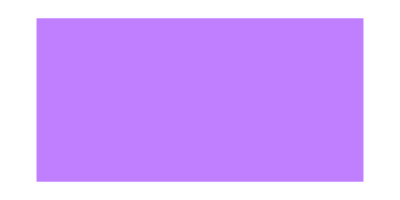

```mathematica
Graphics[{RGBColor[0.5,0,5,0.5],Rectangle[{1,1},{3,2}],Text[""]}]
```

### Fig[zu-graph]

```mathematica
g=Graph[{a,b,c,d},{UndirectedEdge[a,c],UndirectedEdge[a,b],UndirectedEdge[a,d],UndirectedEdge[c,d]}]
```

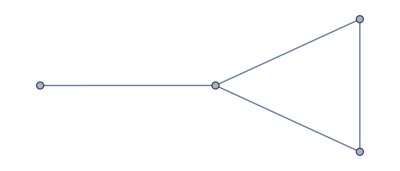

Set::write: Inherited["State"]のタグInheritedはProtectedです．

```mathematica
AdjacencyMatrix[g]//Normal//MatrixForm//TeXForm
```

\left(
\begin{array}{cccc}
 0 & 1 & 1 & 1 \\
 1 & 0 & 0 & 0 \\
 1 & 0 & 0 & 1 \\
 1 & 0 & 1 & 0 \\
\end{array}
\right)

### Fig[zu-ca]

```mathematica
l1=1; l0=0.75
```

0.75

```mathematica
t1=Text[Grid[{{0,0,0}},Frame->All],{0,l1}]
```

Text[0 | 0 | 0,{0,1}]

```mathematica
t2=Text[Grid[{{0,0,1}},Frame->All],{1,l1}]
```

Text[0 | 0 | 1,{1,1}]

```mathematica
t3=Text["...",{2,l1}]
```

Text[...,{2,1}]

```mathematica
t4=Text[Grid[{{1,1,1}},Frame->All],{3,l1}]
```

Text[1 | 1 | 1,{3,1}]

```mathematica
t5=Text[0,{0,l0}]
```

Text[0,{0,0.75}]

```mathematica
t6=Text[0,{1,l0}]
```

Text[0,{1,0.75}]

```mathematica
t8=Text[0,{3,l0}]
```

Text[0,{3,0.75}]

```mathematica
t9=Text["近傍セル",{3.8,l1},{-1,0}]
```

Text[近傍セル,{3.8,1},{-1,0}]

```mathematica
t10=Text["次のセル状態",{3.8,l0},{-1,0}]
```

Text[次のセル状態,{3.8,0.75},{-1,0}]

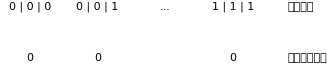

```mathematica
zuca=Graphics[{FontSize->12,t1,t2,t3,t4,t5,t6,t8,t9,t10}]
```

```mathematica
Export["zu-ca.eps",zuca]
```

zu-ca.eps